## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=10 TeV, C_ν_Ri^Z'≈ 0.5

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime10=10;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
e^2/(sinsquared(1-sinsquared))
```

0.515835

```mathematica
Zprime10decaymassless05=MassZprime10/(12π)((gVZp05)^2+(gAZp05)^2)*10^3
```

66.2975

```mathematica
Zprime10decaymassless05plot=MassZprime10/(12π)((GVZp05)^2+(GAZp05)^2)*10^3;
```

```mathematica
Plot3D[Zprime10decaymassless05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=8 TeV, C_ν_Ri^Z'≈ 0.5

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime8=8;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
Zprime8decaymassless05=MassZprime8/(12π)((gVZp05)^2+(gAZp05)^2)*10^3
```

53.038

```mathematica
Zprime8decaymassless05plot=MassZprime8/(12π)((GVZp05)^2+(GAZp05)^2)*10^3;
```

```mathematica
Plot3D[Zprime8decaymassless05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=5 TeV, C_ν_Ri^Z'≈ 0.5

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime5=5;
```

```mathematica
gVZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(0.5))
gAZp05=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.499936

-0.0000644793

```mathematica
Zprime5decaymassless05=MassZprime5/(12π)((gVZp05)^2+(gAZp05)^2)*10^3
```

33.1487

```mathematica
Zprime5decaymassless05plot=MassZprime5/(12π)((GVZp05)^2+(GAZp05)^2)*10^3;
```

```mathematica
Plot3D[Zprime5decaymassless05plot,{GVZp05,0,1},{GAZp05,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Compare Change in Z-Prime mass

```mathematica
Zprime10decaymassless05
Zprime8decaymassless05
Zprime5decaymassless05
```

66.2975

53.038

33.1487

```mathematica
Zprimedecay05[Mz_]:=Mz/(12π)((gVZp05)^2+(gAZp05)^2)*10^3
```

```mathematica
Zprimedecay05[5]
Zprimedecay05[6]
Zprimedecay05[7]
Zprimedecay05[8]
Zprimedecay05[9]
Zprimedecay05[10]
Zprimedecay05[11]
Zprimedecay05[12]
```

33.1487

39.7785

46.4082

53.038

59.6677

66.2975

72.9272

79.5569

```mathematica
DecayTable05=TableForm[{{5,Zprimedecay05[5]},{6,Zprimedecay05[6]},{7,Zprimedecay05[7]},{8,Zprimedecay05[8]},{9,Zprimedecay05[9]},{10,Zprimedecay05[10]},{11,Zprimedecay05[11]},{12,Zprimedecay05[12]}},TableHeadings-> {None,{"TeV","Decay Rate(GeV)"}}]
```

TeV | Decay Rate(GeV)
5 | 33.1487
6 | 39.7785
7 | 46.4082
8 | 53.038
9 | 59.6677
10 | 66.2975
11 | 72.9272
12 | 79.5569

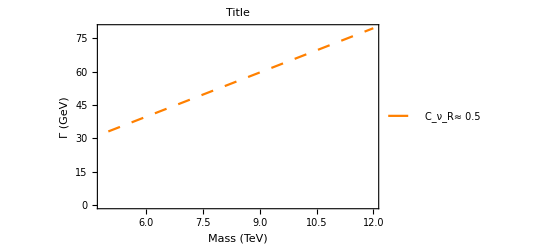

```mathematica
PlotZprimeDecay05=ListPlot[%, Joined-> True,PlotStyle->{Orange,Dashing[Medium]},PlotLegends->{" C_ν_R≈ 0.5"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## *Note each end result is multiplied by 10^3to bring Decay Rate units in MeV